```mathematica
(*Defining constants*)
```

```mathematica
clight=299792458;
G=6.67408*^-11;
```

```mathematica
(*The critical mass density*)
ρcrit=(3 H0^2)/(8*π*G);
```

```mathematica
(*The critical energy density ρcrit*c^2*)
ρcritE=(3 H0^2*clight^2)/(8*π*G);
```

```mathematica
(*The mass of the sun in SI units*)
Msun=1.98855*^30;
```

```mathematica
(*Components of the energy density of the universe radiation mass and owing to the cosmological constant*)
Ωr=9.061*^-5;
Ωm=0.308;
Ωλ=0.692;
```

```mathematica
(*The age of the universe in sec*)
t0=(14*^9)*3.154*10^7;
```

```mathematica
(*The Hubble constant*)
H0=0.678*(9.777752*10^9*3.154*10^7)^-1;
```

```mathematica
(*Parameters for the power spectrum relative to the frequency of the gravitational wave*)
a={2.9740*^-1,5.9411*^-1,5.0801*^-1,8.4845*^-1};
b={4.4810*^-2,8.9794*^-2,7.7515*^-2,1.2848*^-1};
c={9.5560*^-2,1.9111*^-1,2.2369*^-2,2.7299*^-1};
ν1=ν[1];
ν2=ν[2];
σ=ν[3];
ν3=ν[4];
ω1=ν1^-1;
ω2=ν1^-1*ν2^(-4/3);
Ω23=1.3*^-7;
```

```mathematica
(*Mass Components*)
(*We have an equal mass binary so Mtot = 2*Mass of each black hole*)
Mtot=2*M;
```

```mathematica
(*The symmetric reduced mass, η=m1+m2/(m1+m2)^2. If m1=m2,η=1/4*)
η=1/4;
```

```mathematica
(*The chirp mass of the binary*)
Mc=(M^2*(2M)^(-1/3))^(3/5);
```

```mathematica
(*Functions*)
(*Time functions*)
(*Energy used in the time integral related to the dominating factor owing to the density of the universe a given time. Relative to z*)
Energy[z_]:=(Ωr(1+z)^4+Ωm*(1+z)^3+Ωλ)^(1/2)
```

```mathematica
(*The full integral used in the time function, using numericQ because Mathematica does not deal well with symbols in the bounds of integrals*)
INTtime[z_?NumericQ]:=NIntegrate[1/((1+zz)*Energy[zz]),{zz,0,z}]
```

```mathematica
(*Function to find the time in seconds at a given redshift.*)
time[z_?NumericQ]:=t0-1/H0 INTtime[z];
```

```mathematica
(*Frequency function in SI units for our 4 cases of the coefficients a, b, and c*)
ν[i_]:=(a⟦i⟧*η^2+b⟦i⟧*η+c⟦i⟧)/(π*Mtot)*clight^3/G
```

```mathematica
(*The most probably X value of a PBH binary for a given fpbh, mass and time in the universe*)
Xstarall[f_,σ_,m_,t_]:=0.032*f*m^(5/37)*(t/t0)^(3/37)*(f^2+σ^2)^(-21/74)
```

```mathematica
(*The density of matter for a given redshift*)
ρm[z_]:=Ωm*(1+z)^3*ρcrit;
```

```mathematica
(*The full merger rate of primordial black holes for a given redshift, mass of pbh's in the binary and fraction of dark matter in the form of pbhs. Converted to SI units. Note the multiplication by 1/(1+z)^3 to convert to the comoving volume.*)

R[z_?NumericQ,M_,f_]:=0.042*Xstarall[f,0.005,M/Msun,time[z]]*(f*ρm[z])/(M*time[z])1/(1+z)^3
```

```mathematica
(*Mathematica does not deal with symbols in the terminals of integrals and the full integration method is very slow. So we use Simpsons sum to evaluate the integrals with ample step sizes for speed and accuracy.*)

SimpsonsSum[g_,n_,a_,b_,M_,f_,ν_]:=Module[{width=(b-a)/n,coefficient},coefficient[i_?EvenQ]=2;
coefficient[i_?OddQ]=4;
N[width/3*(g[a,M,f,ν]+g[b,M,f,ν]+Sum[coefficient[i]*g[a+i*width,M,f,ν],{i,1,n-1}])]];
```

```mathematica
(*The integral that we need to evaluate in (52) in SI units with the peice wise function 
for the various cases of ν*)
FullInt[z_?NumericQ,M_,f_,ν_]:=R[z,M,f]/((1+z)*Energy[z])*9.337478193506541*^-8 M^(5/3) Piecewise[{{1/((1+z) ν)^(1/3),(1+z) ν<(8.054065748921541*^33)/M},{1.2416089353801245*^-34 M ((1+z) ν)^(2/3),(8.054065748921541*^33)/M≤(1+z) ν<(1.6107513066388488*^34)/M},{(3.052203642378363*^-80 (1+z)^2 ν^2)/((1/M)^(7/3) (1+1.7935886714971486*^-67 M^2 (-(1.6107513066388488*^34/M)+(1+z) ν)^2)^2),(1.6107513066388488*^34)/M≤(1+z) ν<(2.3011312372919675*^34)/M}}]
```

```mathematica
(*We evaluate the above integral and multiply it by the constants of (52) in SI units to obtain the SGWB*)
ΩSimpson[ν_,M_,f_,a_,b_,n_]:=ν/(H0*ρcritE)*SimpsonsSum[FullInt,n,a,b,M,f,ν]
```

```mathematica
(*The inferred SGQB for a given frequency from O1 of LIGO, we compare this with ΩSimpson to obtain the minimum fpbh.*)

ΩGWMax23[ν_]:=Ω23(ν/25)^(2/3)
```

```mathematica
Data2=Table[{ν,ΩSimpson[ν,2000000000000000000000000000000 2^(1/5),0.06,0,10,20]},{ν,10,10^5,1000}];
ListLogLogPlot[Data2];
```

```mathematica
Data3=Table[{ν,ΩSimpson[ν,2.2973967099940697*^29,0.06,0,10,20]},{ν,10,10^5,1000}];
ListLogLogPlot[Data3];
```

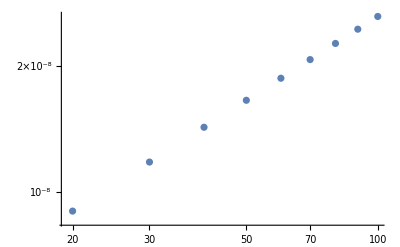

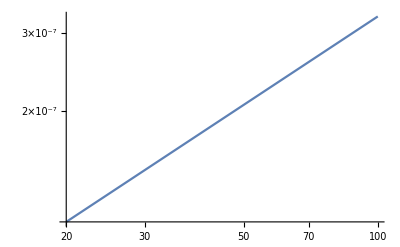

```mathematica
(*We then plot ΩSimpson against ΩGWMax23 for a given mass pbh binary, and vary fpbh untill ΩSimpson falls very slightly below ΩGWMax23 to obtain the maximum fpbh can be for that given mass*)
Data5=Table[{ν,ΩSimpson[ν,0.2*2*^30,0.81/0.85,0,10,20]},{ν,20,100,10}];
ListLogLogPlot[Data5]
Show[LogLogPlot[ΩGWMax23[ν],{ν,20,100}],ListLogLogPlot[Data5]]
```